```mathematica
NS["maxent_binomial_approx","C:\\Users\\pglpm\\repositories\\maxNt\\scripts"]
```

```mathematica
const=Integrate[Exp[-x^2/2],{x,0,1}]
```

√(π/2) Erf[1/(√2)]

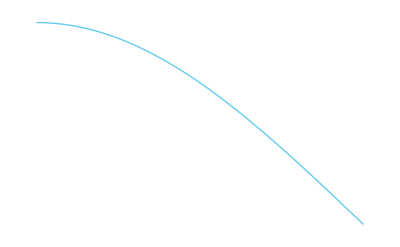

```mathematica
Plot[Exp[-x^2/2]/const,{x,0,1},PlotRange->All]
```

```mathematica
Integrate[Exp[-x^2/2+a*x+b*x^2]/const,{x,0,1}]
```

(ⅇ^(a^2/(2-4 b)) (-Erfi[a/(√(-2+4 b))]+Erfi[(-1+a+2 b)/(√(-2+4 b))]))/(√(-1+2 b) Erf[1/(√2)])